Algorithms

## Introduction

In this chapter we supplement the discussion of algorithms presented in the text with their implementation in Mathematica. In Section 3.1, we discuss the process of turning step-by-step instructions describing a procedure and pseudocode for a procedure into Mathematica code. In the second section, we make use of Mathematica’s graphing capabilities to visualize functions related by the big-O notation. And in Section 3.3, we explore average-case complexity of algorithms by considering the performance of a function on input.

In this chapter, please keep in mind the difference between an algorithm and its implementation (referred to as a function in Mathematica parlance). An algorithm refers to an approach to solving a particular problem, while a function is the implementation of the algorithm within Mathematica. In this manual, we will also distinguish between complexity and performance. Complexity is a measure of an algorithm and is generally measured by counting basic operations such as comparisons, while performance takes into account additional factors related to the specifics of an implementation and can be measured by recording the time it takes for the function to complete. Some of the factors affecting performance may include: choice of data structures and how the system implements those structures, the kinds of loops employed and how those are implemented by the computer language, and various improvements to efficiency handled by the system (for example, many computer languages, when evaluating a Boolean expression such as p∧q, will not bother checking q if p is found to be false thereby decreasing the number of operations that need to be performed).

## 3.1 Algorithms

It is impossible to overemphasize the importance and utility of writing either pseudocode or step-by-step instructions for an algorithm before you write the actual code for the function. Doing so helps you organize your ideas about how to solve the problem without the rigid constraints of the particular programming language. The textbook serves as an excellent model for you as you learn how to turn mathematical concepts and solutions to problems into algorithms. Those algorithms can then be turned into functions in any programming language you choose. This manual will help you turn your pseudocode or step-by-step instructions for algorithms into functions written in Mathematica.

Section 3.1 of the textbook describes several algorithms, with an emphasis on how you can describe these algorithms using both English descriptions and pseudocode. Here, we will see how to implement several of these algorithms in Mathematica. In this chapter, it will be especially important for you to have the text alongside you, as we will not reproduce the descriptions of the algorithms from the text.

### Find Maximum

The first algorithm we will implement is the algorithm for finding the maximum in an unsorted sequence. This is described in Section 3.1 in the solution to Example 1 as step-by-step instructions and as pseudocode in Algorithm 1. We will build the function according to the step-by-step instructions. In order to make the connection between the instructions and the code as clear as possible, we’ll begin with a function with no statements and successively revise it to show the addition of each step. Be warned that the incomplete versions of the function may produce errors, if you execute the definitions.

We begin with the basic elements of the function definition without code. Specifically, we include the name of the function, a pattern to impose the type of the argument, and, since we will have local variables, the Module function and its basic structural elements.

findMax[L:{__Integer}]:=Module[{},

]

Note that the pattern specifying the type of the argument indicates that the function will accept a list (indicated by the braces) which consists of a sequence (indicated by the BlankSequence (_ _)) of at least one integer. The L: means that the argument will be referred to as L.

Step 1 in the step-by-step instructions is to “set the temporary maximum equal to the first integer” in the list. We declare a local variable to store the temporary maximum and add a statement in the body of the function to assign the first integer in the list to this value.

findMax[L:{__Integer}]:=Module[{tempMax},
tempMax=L[[1]];

]

Step 2, according to Example 1 of the text, is to compare the next integer to the temporary maximum and update the temporary maximum if necessary. This requires an If statement to make the comparison.

findMax[L:{__Integer}]:=Module[{tempMax},
tempMax=L[[1]];
If[tempMax<L[[2]],tempMax=L[[2]]];

]

(We are intentionally following the step-by-step instructions to the letter, so in step 2, “the next integer” is L[2].)

Step 3 tells us to repeat step 2 for all of the integers in the list. We need to revise our code as follows. The fact that we are supposed to repeat step 2 means that we’ll need a loop. And since this loop is supposed to consider all of the elements of the list beyond the first means that we use a For loop over the indices of the list starting at 2. We put the code we wrote for step 2 inside this loop, since that’s the instruction being repeated, and replace the specific index “2” with the loop variable. Finally, the loop variable needs to be added to the list of Module variables.

findMax[L:{__Integer}]:=Module[{tempMax,i},
tempMax=L[[1]];
For[i=2,i≤Length[L],i++,
If[tempMax<L[[i]],tempMax=L[[i]]]
];
]

Finally, step 4 tells us that once the loop is completed, the value of the temporary maximum is the maximum, so we return that value.

```mathematica
findMax[L:{__Integer}]:=Module[{tempMax,i},
tempMax=L[[1]];
For[i=2,i≤Length[L],i++,
If[tempMax<L[[i]],tempMax=L[[i]]]
];
tempMax
]
```

```mathematica
findMax[{3,18,-5,72,6,0}]
```

72

Admittedly, this example may be a bit too simple to warrant such an elaborate process. But it illustrates an essential point: a well-written set of step-by-step instructions describing a procedure can be easily turned into working and correct code. Moreover, for non-trivial algorithms, the two-step process of writing instructions for the function and then implementing the function based on those instructions typically results in the production of a correct implementation more quickly than attempting the implementation without writing instructions.

Take a moment to compare the function above with the pseudocode given in Algorithm 1 in the textbook. You will notice that, in this example, they are extremely similar. This is one of the benefits of pseudocode in comparison to step-by-step instructions. However, step-by-step instructions are often easier to write as a first step towards a working function. Step-by-step instructions are also typically easier to understand, especially for novice programmers, as they can more easily accommodate explanation and other information that is out of place in pseudocode.

### Binary Search

The second example will be the binary search algorithm, presented as Algorithm 3 in Section 3.1. The previous example showed how you can use step-by-step instructions to build up the function. Starting from pseudo-code, writing the final implementation involves translating statements in the pseudocode into legal statements in the programming language and filling in missing details.

As before, we will go through several iterations as we translate the pseudocode in the text to actual Mathematica code. Initially, we need to: make sure that the input is specified in a way appropriate for Mathematica; declare the local variables that are indicated in the pseudocode; and make basic syntax adjustments, specifically the while loops, if statements, and mathematical expressions such as ⌊(i+j)/2⌋ must be translated into their Mathematica counterparts.

```mathematica
binarySearch[x_Integer,A:{__Integer}]:=Module[{i,j,m,location},
i=1;
j=n;
While[i<j,
m=Floor[(i+j)/2];
If[x>A[[m]],
i=m+1,
j=m
]
];
If[x==A[[i]],
location=i,
location=0
];
location
]
```

It is too much to expect this first version to properly execute.

```mathematica
binarySearch[19,{1,2,3,5,6,7,8,10,12,13,15,16,18,19,20,22}]
```

0

The problem is a simple one to correct. The pseudocode used n as the last index of the sequence of integers, so we need to make that assignment in our code.

```mathematica
binarySearch[x_Integer,A:{__Integer}]:=Module[{n,i,j,m,location},
n=Length[A];
i=1;
j=n;
While[i<j,
m=Floor[(i+j)/2];
If[x>A[[m]],
i=m+1,
j=m
]
];
If[x==A[[i]],
location=i,
location=0
];
location
]
```

Now we try running it again.

```mathematica
binarySearch[19,{1,2,3,5,6,7,8,10,12,13,15,16,18,19,20,22}]
```

14

Observe that the only commands that we added were the declaration of local variables, and the assignment of n. We also added additional line breaks to be consistent with the style of code used in this manual. Otherwise, the Mathematica code and pseudocode match very closely. It is, of course, not always quite this straightforward, but well-written pseudocode should contain all the essential elements. Like with proofs, as you become more familiar with pseudocode you will find yourself more comfortable with leaving some details out.

### Bubble Sort

As a final example, we will implement the bubble sort, presented in the text as Algorithm 4 of Section 3.1.

For our first attempt at implementing Algorithm 4, we need to: specify the input, declare the local variables (which can, in part, be gleaned from the pseudocode), and correct the syntax for the for loops and if statements.

bubbleSort[A_List]:=Module[{i,j},
For[i=1,i≤n-1,i++,
For[j=1,j≤n-i,j++,
If[A[[j]]>A[[j+1]],
(*then interchange A[[j]] and A[[j+1]]*)
]
]
]
]

The implementation above gets us close to a correct implementation of the bubble sort algorithm, but there are some problems. The simplest to fix is that n is not defined. You can correct this in one of two ways. Either declare n as a local variable and set it equal to the number of elements of A, or replace the two occurrences of n with Length[A].

bubbleSort[A_List]:=Module[{i,j,n=Length[A]},
For[i=1,i≤n-1,i++,
For[j=1,j≤n-i,j++,
If[A[[j]]>A[[j+1]],
(*then interchange A[[j]] and A[[j+1]]*)
]
]
]
]

The next problem is the instruction in the pseudocode to interchange a_j with a_(j+1). Mathematica contains no interchange function. So we'll either have to make an interchange function that can be used within the bubbleSort function or flesh out the code to interchange the two list elements within bubbleSort itself. We take the first approach here so as to preserve as close a connection as possible between our implementation and the pseudocode.

Before creating an interchange function, however, there is another issue to take into consideration. Namely, in Mathematica, arguments to a function cannot be modified. Instead, we need to copy the parameter to a local variable, both in bubbleSort and in the interchange function we are about to write.

Our interchange function will take two arguments: the list of numbers and the index of the smaller of the two positions to be swapped. It will proceed as follows:

Set a temporary variable equal to the first value to be swapped.

Set the value of the first position equal to the second value.

Set the value of the second position equal to the value stored in the temporary variable.

```mathematica
interchange[L_List,i_]:=Module[{M=L,temp},
temp=M[[i]];
M[[i]]=M[[i+1]];
M[[i+1]]=temp;
M
]
```

Now we update our implementation by: copying the list to a local name and replacing all the occurrences of the parameter with the local variable; applying the interchange function; and ending with the local copy of the list, so that it is the output of the function.

```mathematica
bubbleSort[A_List]:=Module[{i,j,n=Length[A],B=A},
For[i=1,i≤n-1,i++,
For[j=1,j≤n-i,j++,
If[B[[j]]>B[[j+1]],
B=interchange[B,j]
]
]
];
B
]
```

```mathematica
bubbleSort[{3,18,-5,72,6,0}]
```

{-5,0,3,6,18,72}

## 3.2 The Growth of Functions

In this section we will use Mathematica to computationally explore the growth of functions. In particular, we will graph functions in order to visually convince ourselves that the big-O relationship is satisfied. We will also see how to use graphs to determine possible witnesses for the constants C and k in the definition of big-O notation. Since, as the textbook mentions, f(x) is O(g(x)) if and only if g(x) is Ω(f(x)), the techniques we explore in this section apply also to big-Omega and big-Theta notation.

We begin by considering the function f(x)=5 x^3+4 x^2+3x+9. Theorem 1 from Section 3.2 tells us that this is O(x^3), but we will use this function as an example of how you can use Mathematica to find values for C and k such that |f(x)|≤C|g(x)| for all x≥k.

### The Plot Function

First we’ll look at options to the Plot function that will be useful in this context. Let’s start by giving names to the formulas.

```mathematica
f1=5*x^3+4*x^2+3*x+9
```

9+3 x+4 x^2+5 x^3

```mathematica
g1=x^3
```

x^3

Graphing f(x) can be done as simply as calling Plot with the function as the first argument and a specification of the domain as the second. The domain specification is given as a list consisting of the name of the independent variable used in the function, the minimum value, and the maximum value.

For example, to display the graph of f(x) with x ranging from 0 to 10, you enter the following.

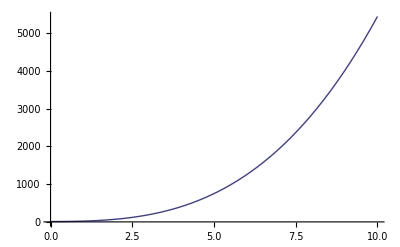

```mathematica
Plot[f1,{x,0,10}]
```

Note that Mathematica automatically selects the vertical range of the graph. You can control this with the PlotRange option. The first two common values for PlotRange are Automatic and All. The Automatic value has the same effect as omitting the option. The difference between Automatic and All is that, in certain circumstances, Mathematica may decide that parts of the function being graphed are outliers and may choose to omit them when using the Automatic plot range. The All value forces Mathematica to display the entire function. This is illustrated below, where we have graphed x^10 with both options.

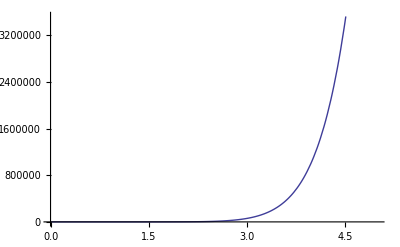
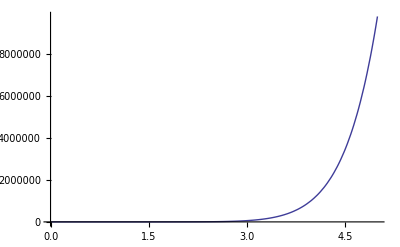

```mathematica
{Plot[x^10,{x,0,5},PlotRange->Automatic],Plot[x^10,{x,0,5},PlotRange->All]}
```

Another common use of PlotRange is to explicitly specify the maximum and minimum y values. If you provide a single positive number as the value for PlotRange, Mathematica will display the graph with that value as the maximum for the vertical axis and its negative as the minimum. The following graphs f(x) with x from 0 to 10 and the vertical axis ranging from -5000 to 5000.

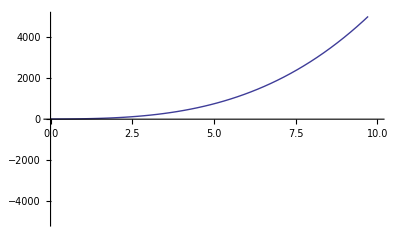

```mathematica
Plot[f1,{x,0,10},PlotRange->5000]
```

If you wish to specify different values for the maximum and minimum for the vertical axis, you can do so with a list consisting of the two values. The following shows f(x) on the domain [0,10] with the vertical axis ranging from -1000 to 5000.

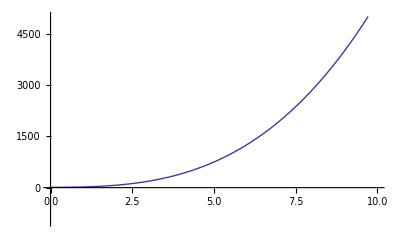

```mathematica
Plot[f1,{x,0,10},PlotRange->{-1000,5000}]
```

Finally, you can use PlotRange to specify the displayed range in both directions using the syntax {{x_min,x_max},{y_min,y_max}}. Note that specifying the range for the horizontal axis in this way is quite different from setting the domain of the function, which is done with the second argument to Plot. We illustrate the difference with the following example.

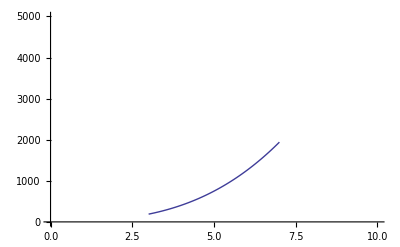

```mathematica
Plot[f1,{x,3,7},PlotRange->{{0,10},{0,5000}}]
```

You can see above that the PlotRange option is specifying the extent of the graph. On the other hand, the second argument, {x,3,7} is a restriction of the domain of the function.

To plot multiple functions in the same graph, use the Plot function with a list of functions as the first argument.

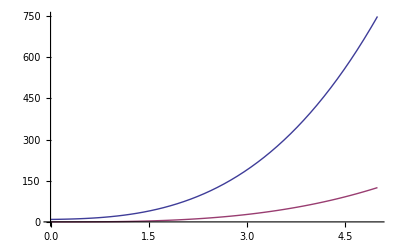

```mathematica
Plot[{f1,g1},{x,0,5}]
```

Note that Mathematica automatically selects colors for the two functions. You can manually select the colors (or other visual effects) with the PlotStyle option. If you use the PlotStyle option with a list of named colors, then the first color will be assigned to the first function, the second color to the second function, and so on. You can choose from common choices such as Red, Green, Blue, Black, White, Gray, Cyan, Magenta, Yellow, Brown, Orange, Pink, and Purple. You can get more information about colors from Mathematica’s Colors guide.

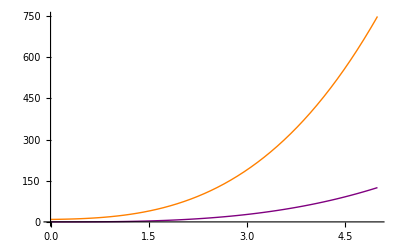

```mathematica
Plot[{f1,g1},{x,0,5},PlotStyle->{Orange,Purple}]
```

When displaying graphs of multiple functions, it can often be useful to include a legend with the graph indicating which function is which. In Mathematica, you can use the PlotLegends option to do this.

PlotLegends is an option to Plot (and other plotting functions such as ListPlot). We will describe three of the possible values.

The simplest way to create a legend is by setting the PlotLegends option to Automatic. This will create a legend that identifies the colors used in the plot with the index of the function.

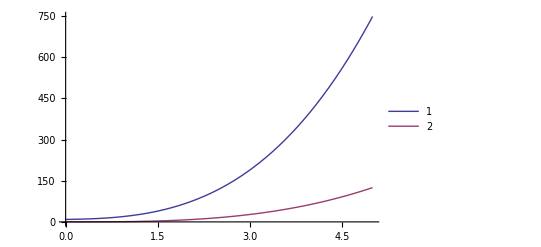

```mathematica
Plot[{f1,g1},{x,0,5},PlotLegends->Automatic]
```

Setting the PlotLegends option to “Expressions” is much more descriptive, showing the expression that is being graphed.

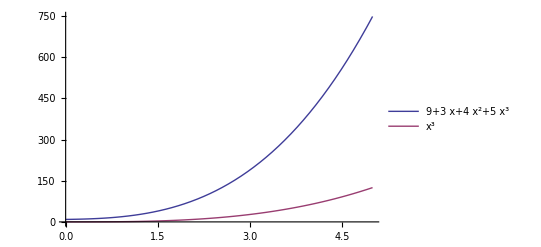

```mathematica
Plot[{f1,g1},{x,0,5},PlotLegends->"Expressions"]
```

Finally, you can specify your own labels by assigning the option to a list containing the expressions to use to identify the functions.

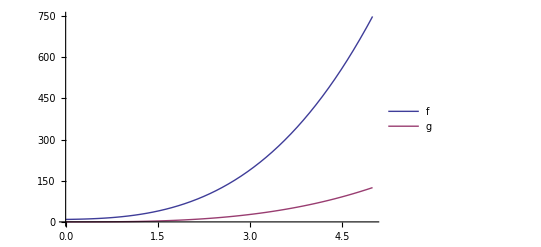

```mathematica
Plot[{f1,g1},{x,0,5},PlotLegends->{"f","g"}]
```

Mathematica provides other possible values for the PlotLegends option to influence the placement of the legend. It also has more general functions, particularly LineLegend, that gives you the ability to completely customize the content and format of the legend.

### Finding Values for C and k

Now we can start exploring different values of C for which the equation f(x)≤C·g(x) is satisfied. To do this, we just have to multiply g1 by different values. We will choose several values until we see a clear crossing.

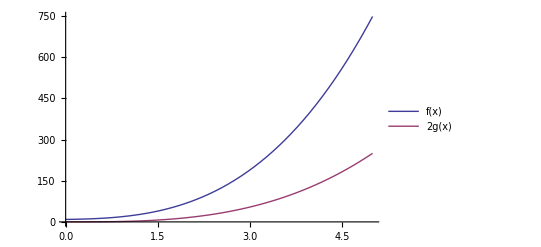

```mathematica
Plot[{f1,2*g1},{x,0,5},PlotLegends->{"f(x)","2g(x)"}]
```

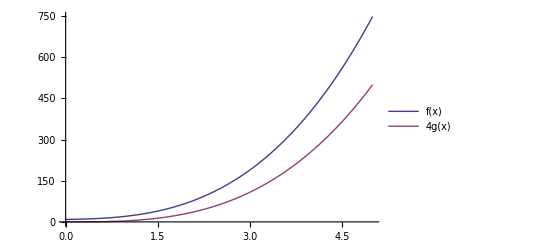

```mathematica
Plot[{f1,4*g1},{x,0,5},PlotLegends->{"f(x)","4g(x)"}]
```

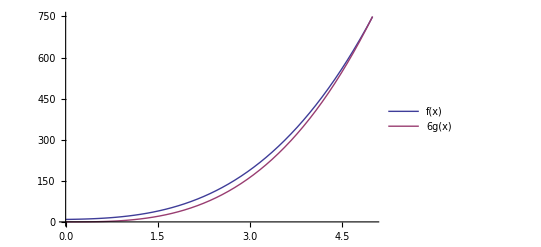

```mathematica
Plot[{f1,6*g1},{x,0,5},PlotLegends->{"f(x)","6g(x)"}]
```

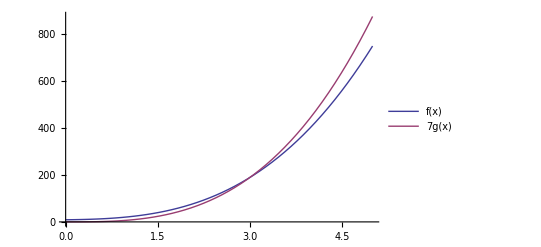

```mathematica
Plot[{f1,7*g1},{x,0,5},PlotLegends->{"f(x)","7g(x)"}]
```

By expanding the range of x values, we can obtain a graph that provides fairly convincing evidence that C=7 and k=3 witness for the assertion that f(x) is O(x^3).

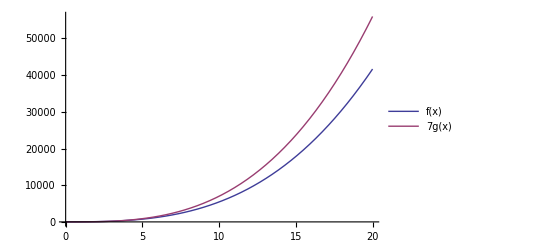

```mathematica
Plot[{f1,7*g1},{x,0,20},PlotLegends->{"f(x)","7g(x)"}]
```

It is important to note that the graph above is not proof that 5 x^3+4 x^2+3x+9 is O(x^3). A formal proof must follow the model provided by the examples in the text.

### A Second Example

As a second example, consider f(x)=3 x^5+x^3 ln(x^2+2x+1). We claim that this is O(x^n) for some value of n. We want to first determine the smallest value of n and then find witnesses for C and k. We assign a name for the formula for f(x). Note that the Mathematica function Log with one argument computes the natural (base e) logarithm of the argument.

```mathematica
f2=3*x^5+x^3*Log[x^2+2*x+1]
```

3 x^5+x^3 Log[1+2 x+x^2]

We could proceed as in the previous example and display a selection of graphs comparing f2 and x^n for different exponents in order to find a likely choice of n and then explore the coefficients. However, Mathematica’s Manipulate function provides an interactive approach. The syntax for a Manipulate is very similar to that of Table. The first argument is an expression involving one or more variables that will be altered by sliders or other controls. In this case, the first argument will be the Plot function.

Following the first argument, we specify the variables that are to be manipulated. In this example, we need to modify the exponent n and the coefficient c. For the exponent, the variable n should be allowed to range from 1 to some arbitrary maximum, say 20. Also, the exponent should be an integer, so we specify a step of 1. Thus the range specification for the exponent will be {n,1,20,1}. Note that the requirement that we include the step of 1 is the main difference between a Table and the Manipulate, which defaults to a continuous range of values. For the coefficient c, we will allow it to range from 1 to 30 continuously, making its specification {c,1,30}.

```mathematica
Manipulate[Plot[{f2,c*x^n},{x,0,5},PlotRange->{0,10000},PlotLegends->{"f","cx^n"}],{n,1,20,1},{c,1,30}]
```

Note that the PlotRange option is useful here. Without it, Mathematica would continually resize the graph depending on the choices for the variables.

When you first execute the Manipulate, you will see only the graph of f(x) since 1·x^1 is too small and lies along the x axis. To inspect the values of n and C, you can click on the small plus symbols on the right of the sliders.

As you use Manipulate to explore this problem, keep in mind that you are searching for the smallest n for which f(x) is O(x^n). So once you find an n and C that work, decrease n and make sure that no C will do. You may need to expand the domain to be sure.

## 3.3 Complexity of Algorithms

Section 3.3 of the textbook emphasizes worst-case complexity of algorithms and shows you how the worst-case complexity can be deductively determined. The textbook also mentions average-case complexity and shows how to compute the average-case complexity of the linear search algorithm (Example 4).

Average-case complexity is typically difficult to analyze deductively, but is still very important. From a practical standpoint, average-case complexity can help differentiate algorithms whose worst-case complexities are of the same order. Also, algorithms that have very poor worst-case complexity may have reasonable average-case complexity, provided that the “bad” inputs that produce the worst case are rare.

While average-case complexity is difficult to analyze, average-case performance can be computed fairly directly. Recall from the introduction to this chapter that we distinguish complexity of an algorithm from performance of a function. In this section we will see how Mathematica can be used to analyze average-case performance of functions experimentally. We will use the bubbleSort function developed in Section 3.1 of this manual as an example. Our goal will be to produce a graph displaying the empirically determined average-case time performance of the procedure.

First we review the standard approach to timing functions in Mathematica. The Timing function takes one argument. It evaluates the expression (e.g., a function applied to input) and returns a 2-element list consisting of the time (in seconds) used and the result of the evaluation.

Here is an example of the use of the Timing function.

```mathematica
Timing[findMax[Range[10000]]]
```

{0.02631,10000}

Note that, in this example, the time that is reported includes the time take by the Range function to produce the list of integers from 1 to 10000. On the other hand, the Timing function does not include any time used in generating or formatting output. This is negligible in this example, but for functions with lengthy or complex output, it is reassuring that this time is not being included.

### Average Input

By average-case performance, we mean the average performance of a function on a random input selected from all possible inputs of the given size. The particulars of how the random input is selected is a necessary component in the analysis. It is natural to assume that each possible input will appear with the same likelihood as every other, but it is important to recognize that this may not always be the case. It may be that, in the circumstances under which the algorithm is intended to be used, some inputs may appear with relatively higher or lower frequency.

In our test of bubbleSort, we have no particular application in mind and so will assume that all inputs are equally likely. In order to generate a random input, we will use the RandomSample function applied to the list produced by Range. The RandomSample function applied to a list produces a rearrangement of that list. The following produces a list of the first five positive integers in random order.

```mathematica
RandomSample[Range[5]]
```

{1,5,3,2,4}

We can apply the bubbleSort algorithm directly to the result and time how long it takes to execute. Note that we obtain the time, without the output from bubbleSort, by accessing the first element of the list output by Timing.

```mathematica
Timing[bubbleSort[RandomSample[Range[20]]]][[1]]
```

0.00199

Since we are after average-case performance, we'll want to execute bubbleSort on some, say 100, different random inputs and average the time taken by each execution. To collect the 100 times, we can use a Do loop to repeatedly execute the function. We use Sow and Reap to build the list of times, with Sow applied to the result of Timing and Reap surrounding the loop. Recall that the first entry in the list output by Reap is the output of its argument. Since the argument to Reap is Do, which has no output, the first element of the output will be Null. The second element of the output from Reap is the list of lists sown by Sow. So we will be able to access the list of times as the [[2,1]] element of the output from Reap.

```mathematica
timesExampleReap =Reap[
Do[
Sow[
Timing[bubbleSort[RandomSample[Range[20]]]][[1]]
],
{100}]
]
```

{Null,{{0.00188,0.00216,0.00186,0.00146,0.00167,0.00162,0.00194,0.0019,0.00149,0.00225,0.00194,0.00203,0.002,0.00183,0.00131,0.00182,0.00186,0.00194,0.00166,0.0018,0.00148,0.00189,0.00187,0.00162,0.00228,0.00194,0.0017,0.00205,0.00191,0.00213,0.00197,0.00216,0.00164,0.00214,0.00222,0.00194,0.0019,0.00188,0.00202,0.00166,0.0015,0.00174,0.00194,0.00157,0.00176,0.00181,0.00179,0.00183,0.00203,0.00156,0.00181,0.0018,0.00172,0.00144,0.00194,0.002,0.00189,0.00197,0.00159,0.00194,0.00183,0.00189,0.00176,0.00158,0.00167,0.00186,0.0018,0.00177,0.00201,0.00169,0.00184,0.00161,0.00203,0.00192,0.00191,0.00178,0.00178,0.00196,0.00191,0.00202,0.00167,0.00199,0.00195,0.00205,0.00204,0.0018,0.0017,0.00161,0.00163,0.00194,0.00231,0.0018,0.00145,0.00186,0.00167,0.00181,0.00196,0.0015,0.00181,0.00176}}}

```mathematica
timesExample=timesExampleReap[[2,1]]
```

{0.00188,0.00216,0.00186,0.00146,0.00167,0.00162,0.00194,0.0019,0.00149,0.00225,0.00194,0.00203,0.002,0.00183,0.00131,0.00182,0.00186,0.00194,0.00166,0.0018,0.00148,0.00189,0.00187,0.00162,0.00228,0.00194,0.0017,0.00205,0.00191,0.00213,0.00197,0.00216,0.00164,0.00214,0.00222,0.00194,0.0019,0.00188,0.00202,0.00166,0.0015,0.00174,0.00194,0.00157,0.00176,0.00181,0.00179,0.00183,0.00203,0.00156,0.00181,0.0018,0.00172,0.00144,0.00194,0.002,0.00189,0.00197,0.00159,0.00194,0.00183,0.00189,0.00176,0.00158,0.00167,0.00186,0.0018,0.00177,0.00201,0.00169,0.00184,0.00161,0.00203,0.00192,0.00191,0.00178,0.00178,0.00196,0.00191,0.00202,0.00167,0.00199,0.00195,0.00205,0.00204,0.0018,0.0017,0.00161,0.00163,0.00194,0.00231,0.0018,0.00145,0.00186,0.00167,0.00181,0.00196,0.0015,0.00181,0.00176}

(Depending on the speed of your computer, you may need to increase the size of the input list in order to get non-zero times.)

To average the times, we apply the Mean function to the list of values.

```mathematica
Mean[timesExample]
```

0.00183

### Graphing the Empirically Calculated Average-case Complexity

To graph the average time data, we’ll use the ListPlot function, discussed in Section 2.3 of this manual. Recall that ListPlot takes as its argument a list of lists where the sublists are x-y pairs.

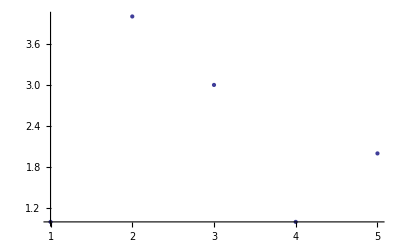

```mathematica
ListPlot[{{1,1},{2,4},{3,3},{4,1},{5,2}}]
```

We will now write a function that produces the list of data required by ListPlot. This function will compute the average, over a number of trials, of the time taken to execute bubbleSort on randomly generated lists of size 10, 20, 30, 40, and 50.

```mathematica
getBubbleTimes[trials_Integer,min_Integer,max_Integer,step_Integer]/;trials>0&&min>0&&max>min&&step>0:=Module[{s,avgTimeData={},times,input},
For[s=min,s≤max,s=s+step,
times=Reap[
Do[
input=RandomSample[Range[s]];
Sow[Timing[bubbleSort[input]][[1]]],
{trials}]
][[2,1]];
AppendTo[avgTimeData,{s,Mean[times]}]
];
avgTimeData
]
```

Most of the function is enclosed in the For loop with variable s, representing the size of the input that will be passed to bubbleSort. Within the For loop are two statements: the first is an assignment to the symbol times, the right hand side of which spans 6 lines of code, and the second appends the average of the data stored in times to the symbol avgTimeData. The right hand side of the times assignment is where most of the work is done. A Reap encloses this section of code, and times is assigned to the [[2,1]] entry of the output of the Reap, which effectively assigns times to the sown values. Within the Reap is a Do loop, the second argument of which, {trials}, indicates that the body of the Do loop will be executed a number of times dictated by the argument to the function. There is no need for a loop variable. Within the Do loop, the symbol input is assigned to the result of RandomSample applied to the list of positive integers determined by the input size s. Then bubbleSort is applied to this input within Timing and Sow is applied to the time. Note that, unlike our example above, we moved the application of RandomSample and Range outside of the Timing function, so that the time taken to generate the random input is not being included.

Now we execute the function and use the result to create a graph.

```mathematica
bubbleTimes=getBubbleTimes[100,10,50,10]
```

{{10,0.00052},{20,0.00185},{30,0.00418},{40,0.00742},{50,0.01147}}

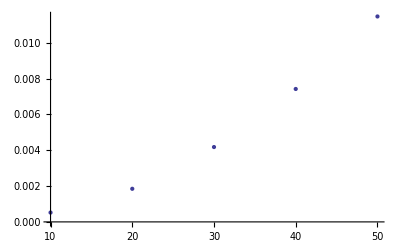

```mathematica
ListPlot[bubbleTimes]
```

From the shape of the graph, it appears that the average-case performance of bubbleSort is polynomial. This suggests that the complexity of the algorithm is also polynomial. Of course, a proof of that fact would require an analysis of the kind given in Example 4 of Section 3.3.

The reader can experiment with the function in order to produce finer detail (by decreasing the step) and to obtain data for larger input lists (by increasing the maximum list size).

We conclude with a caveat. The empirical testing we've done in this section is an example of a way to get an idea of the average-case performance of a procedure. It can be used to compare two or more algorithms with each other and can indicate major differences in worst-case and average-case complexity (for instance, in an algorithm with exponential worst-case complexity and polynomial average-case complexity). But beyond generalities, the implementation of the algorithm, the computer running it, the computer language it is written in, and a host of other factors can play a sufficiently significant role that this approach is generally not helpful for making finer distinctions (between quadratic and cubic complexity, for example).

The reader should refer to the solution of Computer Project 9 below for a method of analyzing average case complexity that modifies the function in order to count the number of operations used with the input values.

## Solutions to Computer Projects and Computations and Explorations

### Computer Project 9

Given an ordered list of n integers and an integer x in the list, find the number of comparisons used to determine the position of x in the list using a linear search and using a binary search.

Solution: There is no loss of generality to assume that the list of n integers is the list of integers from 1 to n.

For the linear search algorithm provided as Algorithm 2 in Section 3.1 of the text, each step in the search requires 2 comparisons, one tests whether the end of the list has been reached and one tests whether the current element is the element being searched for. These are both contained in the Boolean expression that controls the while loop. A final comparison is used after the while loop is completed to determine whether the element was found or not. In the list of n integers 1 through n, the integer x is therefore found after 2x+1 comparisons.

To determine the number of comparisons needed to find x via the binary search algorithm, we'll modify the procedure we wrote in Section 3.1 of this manual to count comparisons. For reference, here is the original binarySearch function.

binarySearch[x_Integer,A:{__Integer}]:=Module[{n,i,j,m,location},
n=Length[A];
i=1;
j=n;
While[i<j,
m=Floor[(i+j)/2];
If[x>A[[m]],
i=m+1,
j=m
]
];
If[x==A[[i]],
location=i,
location=0
];
location
]

We will modify this function to count comparisons. Each time through the While loop accounts for 2 comparisons, the i<j comparison that controls the loop and the x>A[m] comparison in the If statement. So we'll add a line of code to increment the comparison count by 2 at the start of the While loop. Also, we need to add one to the comparison count after the end of the loop to account for the comparison that terminates the loop. And one final comparison is done, in the final If statement, to determine if the search has succeeded or not.

By incrementing the count after the final If statement, the increment will be the final expression and consequently is what will be shown as the result of the function. Here is the modified function.

```mathematica
binarySearchC[x_Integer,A:{__Integer}]:=Module[{n,i,j,m,location,count=0},
n=Length[A];
i=1;
j=n;
While[i<j,
count=count+2;
m=Floor[(i+j)/2];
If[x>A[[m]],
i=m+1,
j=m
]
];
count=count+1;
If[x==A[[i]],
location=i,
location=0
];
count=count+1
]
```

For example, to find 15 in the list from 1 to 20, it takes

```mathematica
binarySearchC[15,Range[20]]
```

10

comparisons.

We can use the information above to compare the average number of comparisons required in a list of n elements. We need to determine the number of comparisons needed to find each value from 1 to n in the list from 1 to n and average these numbers of comparisons. For the linear search, we know that it takes 2x+1 comparisons, so the average can be found from

(∑_(x=1)^n 2x+1)/n

We use Mathematica’s symbolic summation capabilities, specifically the Sum function (discussed in Section 2.4 of this manual).

```mathematica
Sum[2*x+1,{x,1,n}]/n
```

(2 n+n^2)/n

```mathematica
Simplify[%]
```

2+n

(The Simplify function forces Mathematica to simplify expressions.)

For the binary search function, we can find the average by applying our function above to each integer in turn and taking the average. The following function will produce the average number of comparisons required for a given value of n.

```mathematica
binaryAvg[n_Integer]:=Module[{data={},inputList,x},
inputList=Range[n];
data=Reap[
Do[Sow[binarySearchC[x,inputList]],
{x,1,n}
]
][[2,1]];
Mean[data]//N
]
```

The function N is used to obtain an numerical (floating point) value of an exact expression. Without it, Mathematica would return a fraction as the result of this function, but we generally expect means to be reported as floating point numbers.

For example, in the list from 1 to 20, it requires an average of 20+2=22 comparisons using the linear search, and an average of 10.8 comparisons using the binary search.

```mathematica
binaryAvg[20]
```

10.8

Next, we'll graph the average number of comparisons as n ranges from 1 to 100.

For the linear search algorithm, we will graph the function n+2 using Plot. In Section 2.5 of this manual, we demonstrated how to overlay two graphs using the Show function. We will use the same approach here. Keep in mind when doing this that since the two graphs are created separately, the functions will have the same color if you do not specify the color manually using the PlotStyle option.

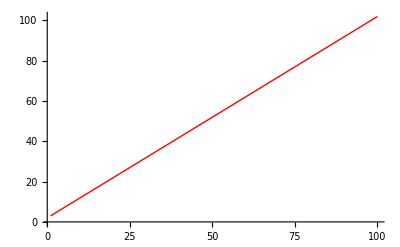

```mathematica
linearSearchGraph=Plot[n+2,{n,1,100},PlotStyle->Red]
```

For the binary search algorithm, we must first create the necessary data before we can graph it with the ListPlot function. Recall from Section 3.2 of this manual that ListPlot requires a list of the x-y pairs given as sublists. The x values will be the values of n.

```mathematica
binarySearchdata=Table[{n,binaryAvg[n]},{n,1,100}];
```

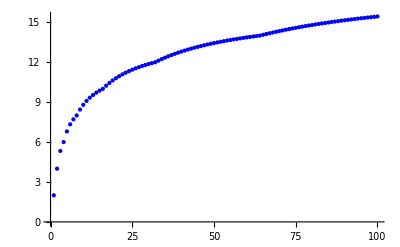

```mathematica
binarySearchGraph=ListPlot[binarySearchdata,PlotStyle->Blue]
```

We overlay the two graphs using Show.

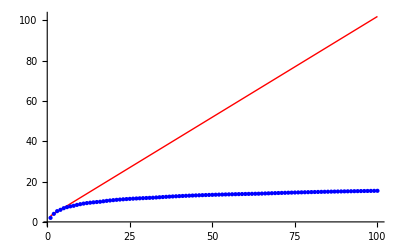

```mathematica
Show[linearSearchGraph,binarySearchGraph]
```

Below we display the same graph using Legended and LineLegend to illustrate some of the additional legending options.

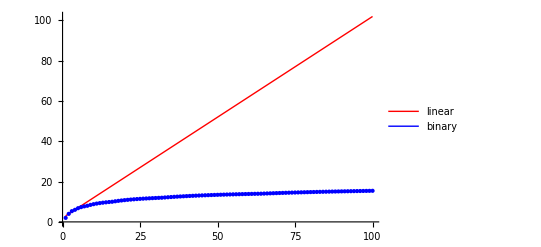

```mathematica
Legended[Show[linearSearchGraph,binarySearchGraph],LineLegend[{Red,Blue},{"linear","binary"},LegendFunction->Framed]]
```

### Computations and Explorations 1

We know that n^b is O(d^n) when b and d are positive numbers with d≥2. Give values of the constants C and k such that n^b≤C·d^n whenever n>k for each of these sets of values: b=10, d=2; b=20, d=3; b=1000, d=7.

Solution: For b=10 and d=2, we need to compare the function f(n)=n^10 to g(n)=2^n. Following the approach we took in Section 3.2, we will use Manipulate to graph the functions while dynamically changing the value of C. Note that the values of C that will suffice with k<20 are extremely large. When exploring other values of b and d, you may have to modify the maximum values for C. It is also possible to find smaller values of C by increasing the horizontal extent of the graph.

```mathematica
Manipulate[Plot[{n^10,c*2^n},{n,0,20},PlotLegends->"Expressions"],{c,0,10^8}]
```

## Exercises

Write step-by-step instructions, then pseudocode, and then implement in Mathematica an algorithm to determine the k largest integers in a list of integers.

Implement the linear search presented as Algorithm 2 in Section 3.1 of the text.

Implement the insertion sort presented as Algorithm 5 in Section 3.1 of the text.

Implement the greedy change-making algorithm presented as Algorithm 6 in Section 3.1 of the text.

Implement the algorithm for scheduling talks presented as Algorithm 7 in Section 3.1 of the text.

Implement the brute-force algorithm for finding the closest pair of points as presented in Algorithm 3 in Section 3.3 of the text.

Modify the bubbleSort function so that it terminates when no more interchanges are necessary. (See Exercise 37 from Section 3.1.)

Implement the selection sort algorithm in Mathematica. (Refer to the preamble to Exercise 41 in Section 3.1 for information on selection sort.)

Implement the binary insertion sort in Mathematica. (Refer to the preamble to Exercise 47 in Section 3.1 for information on the binary insertion sort.)

Implement the deferred acceptance algorithm in Mathematica. (Refer to the preamble to Exercise 61 in Section 3.1 for information on the deferred acceptance algorithm.)

Following the solution to Computations and Explorations 1, use Mathematica to determine values for C and k that witness for the fact that f(x) is O(g(x)) for each of the pairs of functions given below.

f(x)=7·ln(3 x^2-2x+5); g(x)=x

f(x)=x^4/(x^2-4x-4); g(x)=x^2

f(x)=⌊x⌋·⌈x⌉; g(x)=x^2

f(x)=n·ln(n); g(x)=ln(n!)

Using the approach described in Section 3.3 of this manual, compare the average-case performance of the bubbleSort function presented in Section 3.1 to Mathematica's Sort function.

Using the solution to Computer Project 9 as a model, compare the average-case complexity (as measured by number of comparisons) of the bubbleSort function with the modified procedure that you implemented as Exercise 7.

Using the solution to Computer Project 9 as a model, compare the average-case complexity (as measured by number of comparisons) of the bubbleSort function with the other sort procedures you wrote (e.g., insertion sort, selection sort, or binary selection sort).